```mathematica
Clear["Global`*"]
```

## L→∞, N→∞, nearest neighbour approximation

## Dependence on fnn1 and fnn2

```mathematica
Clear[αinf1, αinf2];
```

```mathematica
αinf1 = 1/(1+4fnn1); αinf2 = 1/(1+4fnn2);
Qinf = (-αinf1/2 + 1 - fnn1)(-αinf2/2 + 1 - fnn2)fnn1;
D[Qinf/(-αinf2/2 + 1 - fnn2), fnn1] // Simplify
D[Qinf/(-αinf1/2 + 1 - fnn1)/fnn1, fnn2] // Simplify
```

(1+12 fnn1-64 fnn1^3)/(2 (1+4 fnn1)^2)

-1+2/(1+4 fnn2)^2

```mathematica
D[(-αinf1[fnn1]/2 + 1 - fnn1)fnn1, fnn1] /. {αinf1'[fnn1]-> -4αinf1[fnn1]^2} // Simplify
```

1/2 (2-4 fnn1-fnn1 (-4/(1+4 fnn1)^2)[fnn1]-1/(1+4 fnn1)[fnn1]+4 fnn1 (1/(1+4 fnn1)[fnn1])^2)

```mathematica
fnn2sol = First@Solve[-1+2/(1+4 fnn2)^2==0 && fnn2>0, fnn2]
```

{fnn2→1/4 (-1+√2)}

```mathematica
N[fnn2sol]
```

{fnn2→0.103553}

```mathematica
fnn1sol = FullSimplify/@Solve[(1+12 fnn1-64 fnn1^3)/(2 (1+4 fnn1)^2)==0, fnn1]
```

{{fnn1→1/2 Cos[π/9]},{fnn1→Root[-1-12 #1+64 #1^3&,1]},{fnn1→Root[-1-12 #1+64 #1^3&,2]}}

```mathematica
N[{{fnn1->1/2 Cos[π/9]},{fnn1->Root[-1-12 #1+64 #1^3&,1]},{fnn1->Root[-1-12 #1+64 #1^3&,2]}}]
```

{{fnn1→0.469846},{fnn1→-0.383022},{fnn1→-0.0868241}}

```mathematica
Qinf /. fnn1sol[[1]] /. fnn2sol[[1]] // N
```

0.0909361

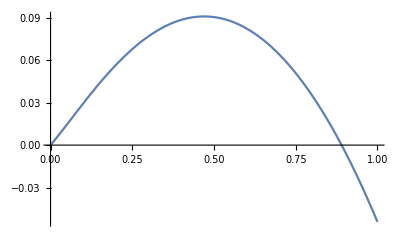

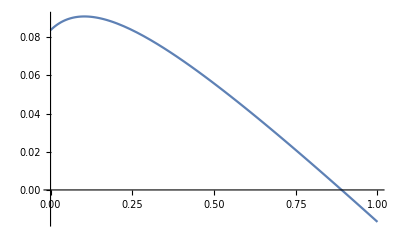

```mathematica
Plot[Qinf /.fnn2sol , {fnn1, 0, 1}]
Plot[Qinf /.fnn1sol[[1]] , {fnn2, 0, 1}]
```

```mathematica
D[(1+12 fnn1-64 fnn1^3)/(2 (1+4 fnn1)^2), fnn1] /. fnn1sol[[1]] // N
```

-1.83244

```mathematica
Plot3D[Qinf, {fnn1, 0,1}, {fnn2, 0, 1}, AxesLabel-> {"(f^1)_nn" ,"(f^2)_nn", "Q"}]
```

-Graphics3D-

Note that global maximum of Q may be unreachable, if fnn1 and fnn2 are taken to depend on a0 with all other parameters fixed. In that case, varying a0 traces out a path on the fnn1-fnn2 plane and the maximum of this path along this plane defines the realizable maximum of Q.

## Dependence on a_0

Study dependence of solutions on a0

```mathematica
params = {R-> 0.2 a0, lambda1 -> 1, lambda2 -> 1.2}
fnnSol = {1/2 Cos[π/9], 1/4 (-1+√2)};
fnn1 = Exp[(R - a0)/lambda1]/(a0/lambda1 )*Sinh[R/lambda1];
fnn2 = Exp[(R - a0)/lambda2]/(a0/lambda2) *Sinh[R/lambda2];
```

```mathematica
Limit[ Exp[- (1-rcell) r]/r Sinh[rcell*r] /. {rcell-> 0.5} , r->∞]
```

0.

```mathematica
Plot [ D[Exp[- (1-rcell) r]/r Sinh[rcell*r], r] /. {rcell-> 0.2}, {r,0.1, 1}]
```

General::ivar: 0.100018 is not a valid variable.

General::ivar: 0.118386 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

-Graphics-

```mathematica
fnn1 /. params
Limit[  fnn1 /. {R-> 0.1 a0, lambda1 -> 1}, a0->0 ]
```

(ⅇ^(-0.8 a0) Sinh[0.2 a0])/a0

0.1

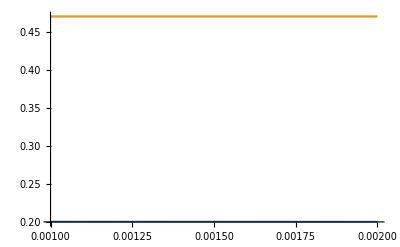

```mathematica
Plot[ {fnn1 /. params, fnnSol[[1]]}, {a0, 0.001, 0.002}]
```

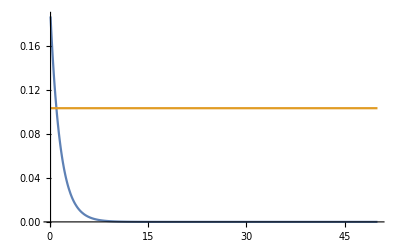

∞

```mathematica
Plot[ {fnn2 /. params, fnnSol[[2]]}, {a0, 0.1, 50}]
```

Plot area fractions as function of a0

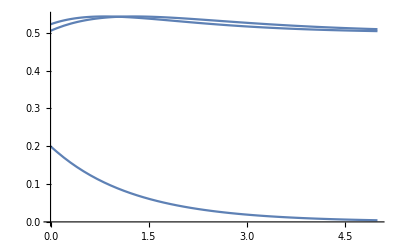

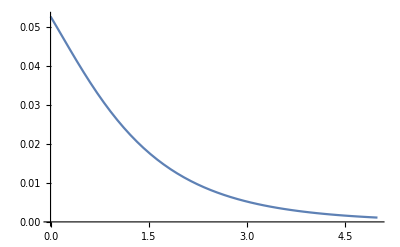

```mathematica
Plot[{(-αinf1/2 + 1 - fnn1),(-αinf2/2 + 1 - fnn2) , fnn1} /. params,  {a0, 0, 5}]
Plot[{(-αinf1/2 + 1 - fnn1)*(-αinf2/2 + 1 - fnn2) * fnn1} /. params,  {a0, 0, 5}]
```

Find constrained maximum at fixed parameter values as a function of a0

```mathematica
Qinf = (-αinf1/2 + 1 - fnn1)(-αinf2/2 + 1 - fnn2)fnn1;
αinf1 = 1/(1+4fnn1); αinf2 = 1/(1+4fnn2);
fnn1 = Exp[(R - a0)/lambda1]/(a0/lambda1 )Sinh[R];
fnn2 = Exp[(R - a0)/lambda2]/(a0/lambda2)  Sinh[R];
```

```mathematica
Solve[( D[Qinf, a0]  == 0)/.params , a0 ]
```

$Aborted

{R→0.2 a0,lambda1→1,lambda2→1.2}

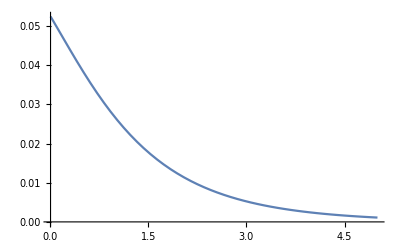

```mathematica
params = {R-> 0.2 a0, lambda1 -> 1, lambda2 -> 1.2}
Plot[ Qinf /. params, {a0, 0.01, 5}]
```

```mathematica
Limit[Qinf /. params, {a0 -> 0}]
```

0.0527338

No maximum observed? Check with MATLAB results

## L→∞, N→∞, mean-field

```mathematica
αinf1 = 1/(1+4fnn1 + fMF1*pW1); αinf2 = 1/(1+4fnn2+ fMF2*pW2);
fnn1 = Exp[(Rcell - a0)/lambda1]/(a0/lambda1 )*Sinh[Rcell/lambda1];
fnn2 = Exp[(Rcell - a0)/lambda2]/(a0/lambda2) *Sinh[Rcell/lambda2];
fMF1 = (4π)/(Sqrt[3] a0^2)*Exp[(Rcell-3/2*a0)/lambda1] Sinh[Rcell/lambda1];
fMF2 = (4π)/(Sqrt[3] a0^2)*Exp[(Rcell-3/2*a0)/lambda2] Sinh[Rcell/lambda2];
Ainf1 = (1+4fnn1 + fMF1*pW1)/2*αinf1^2  - αinf1 - (1-fnn1-fMF1*pW1/2);
Ainf2 = (1+4fnn2 + fMF2*pW2)/2*αinf2^2  - αinf2 - (1-fnn2-fMF2*pW2/2);
Qinf = Ainf1*Ainf2*fnn1;

params = {Rcell -> 0.2 a0, lambda1 -> 1, lambda2 -> 1.2, pW1->2/15, pW2->2/15};
```

```mathematica
Qinf /. {Rcell-> rcell*a0}
```

1/a0 ⅇ^((-a0+R)/lambda1) lambda1 Sinh[R/lambda1] (-1+(ⅇ^((-a0+R)/lambda1) lambda1 Sinh[R/lambda1])/a0+(2 ⅇ^((-(3 a0)/2+a0 rcell)/lambda1) π pW1 Sinh[(a0 rcell)/lambda1])/(√3 a0^2)-1/(2 (1+(4 ⅇ^((-a0+R)/lambda1) lambda1 Sinh[R/lambda1])/a0+(4 ⅇ^((-(3 a0)/2+a0 rcell)/lambda1) π pW1 Sinh[(a0 rcell)/lambda1])/(√3 a0^2)))) (-1+(ⅇ^((-a0+R)/lambda2) lambda2 Sinh[R/lambda2])/a0+(2 ⅇ^((-(3 a0)/2+a0 rcell)/lambda2) π pW2 Sinh[(a0 rcell)/lambda2])/(√3 a0^2)-1/(2 (1+(4 ⅇ^((-a0+R)/lambda2) lambda2 Sinh[R/lambda2])/a0+(4 ⅇ^((-(3 a0)/2+a0 rcell)/lambda2) π pW2 Sinh[(a0 rcell)/lambda2])/(√3 a0^2))))

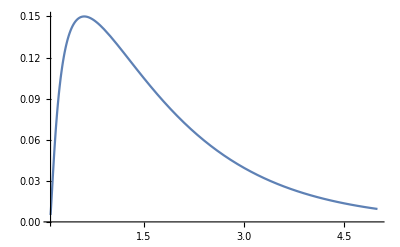

```mathematica
Plot[ Qinf /. params, {a0, 0.1, 5}]
```

```mathematica
Solve[ D[Qinf /. params, a0] == 0, a0]
```

$Aborted

## Auxiliary calculations

Limits

```mathematica
f[ρ_]:= λ/ρ Exp[(rcell-ρ)/λ]Sinh[rcell/λ]
```

```mathematica
Limit[ f[ρ], λ->∞]
```

rcell/ρ

```mathematica
Limit[ 1/(λ(λ+R))Exp[-1/λ], λ->∞]
```

0

```mathematica
TrigToExp[Exp[(rcell-ρ)/λ]Sinh[rcell/λ]]
```

-1/2 ⅇ^(-rcell/λ+(rcell-ρ)/λ)+1/2 ⅇ^(rcell/λ+(rcell-ρ)/λ)

```mathematica
Simplify[-1/2 ⅇ^(-rcell/λ+(rcell-ρ)/λ)+1/2 ⅇ^(rcell/λ+(rcell-ρ)/λ)]
```

1/2 ⅇ^(-ρ/λ) (-1+ⅇ^((2 rcell)/λ))

```mathematica
Limit[l/(2 ρ) ⅇ^(-ρ/l) (-1+ⅇ^((2 rcell)/l)),l-> 0]
```

ConditionalExpression[∞,rcell>0&&2 rcell>ρ&&ρ>0]

Different limits

```mathematica
f[n_]:= λ/(n*a0)Exp[((rcell-n)*a0)/λ]Sinh[rcell*a0/λ]
```

```mathematica
Limit[ f[n], a0-> 0]
```

rcell/n

Inverting f(r)

```mathematica
f[x_] := x^2;
g[x_]:=InverseFunction[ f][x]
```

```mathematica
f[l_]:= Exp[-l]/l*Sinh[l];
g[x_]:=InverseFunction[ f][x];
g[x]
```

f^(-1)[x]

```mathematica
Solve[ Exp[-l]/l*Sinh[l] == y && l>0, l]
TrigToExp[Exp[-l]/l*Sinh[l] ]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[(ⅇ^-l Sinh[l])/l==y&&l>0,l]

1/(2 l)-ⅇ^(-2 l)/(2 l)

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

(1+y ProductLog[-ⅇ^(-1/y)/y])/(2 y)

(1+y ProductLog[-ⅇ^(-1/y)/y])/(2 y)

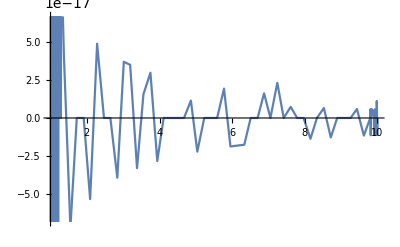

```mathematica
l /.First@Solve[1/(2 l)-ⅇ^(-2 l)/(2 l)==y,l]
finv[y_]:= (1+y ProductLog[-ⅇ^(-1/y)/y])/(2 y);
finv[y]
Plot[finv[y], {y,1, 10}]
```

```mathematica
TrigToExp[Exp[ (rcell-z)/l ]/(z/l) *Sinh[z/l]] /. {l-> finv[y]} // FullSimplify
```

(ⅇ^((2 y (rcell-2 z))/(1+y ProductLog[-ⅇ^(-1/y)/y])) (-1+ⅇ^((4 y z)/(1+y ProductLog[-ⅇ^(-1/y)/y]))) (1+y ProductLog[-ⅇ^(-1/y)/y]))/(4 y z)